## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/andes/LogProcessing/moment-of-learning

```mathematica
journalStyle={FontSize->9 (* ACM default font for text (10 for large journal format) *)};
figureWidth=72 If[False,6.5 (* Maximum allowed width for ACM journal large format. *),
	10/3 (* ACM journal column with for two-column format. *)];
```

```mathematica
data["student"]=Import["guerra-summer-2011-kc-opps.csv"];
```

```mathematica
Take[data["student"],5]
```

{{accel-at-rest,asu_9Q1920841f2ca4d1fasul1_c,md5:1da7d76bc3d524d51da47dde26ee8f95,0,1},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_e,md5:e3e61859acb08ee896e06e1020f95a49,0},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e66c328693800f93b41f13d97b78e19b,1},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e9747bab59caf0446778cc6a65a8ac2e,0}}

```mathematica
Map[Function[x,x.x],Transpose[{{a,b},{c,d}}]-{e,f}]
```

{(a-e)^2+(c-e)^2,(b-f)^2+(d-f)^2}

### Estimate the mode of continuous multi-variate data

This was inspired by the “half - sample mode” method of estimating the mode.  
See http://dl.acm.org/citation.cfm?id=1648101 and http://arxiv.org/abs/math/0505419.  
Unfortunately, this cannot be applied to larger dimensions.

The following is equivalent to mean-shift alogorithm with a flat kernel, in the shape of an ellipsoid or box, depending on the norm chosen.  However, we estimate the center with the median instead of the mean (should be faster convergence).  And we choose the size of the bandwidth parameter h so that some fraction of the points fall inside the kernel.

```mathematica
cutOutlierMode[data_List,test_:False]:=Block[{n=Length[data],c=3 Median[data]-2 Mean[data] (* Using Pearson rule of thumb for mode. *)},If[n<3,Mean[data],If[test,Print[{n,c,Norm[StandardDeviation[data]]}]];
Block[{try=Take[Sort[Map[{Norm[#-c,Infinity],#}&,data],#1[[1]]<#2[[1]]&],Min[n-1,Ceiling[5 n/6]]]},cutOutlierMode[Map[#[[2]]&,try],test]]]]
```

```mathematica
dd=Table[Random[],{100},{2}];
```

```mathematica
cutOutlierMode[dd,True]
```

{100,{0.547103,0.602464},0.408282}

{84,{0.55684,0.66861},0.356774}

{70,{0.569035,0.664454},0.320924}

{59,{0.551702,0.633019},0.288699}

{50,{0.566308,0.642177},0.269353}

{42,{0.574037,0.615927},0.246541}

{35,{0.580398,0.634092},0.230643}

{30,{0.59848,0.582623},0.217892}

{25,{0.589318,0.585254},0.20345}

{21,{0.575856,0.596935},0.181332}

{18,{0.562576,0.601283},0.167756}

{15,{0.594219,0.580113},0.154153}

{13,{0.582852,0.594451},0.14364}

{11,{0.553302,0.585906},0.131457}

{10,{0.563879,0.565166},0.121012}

{9,{0.579815,0.570746},0.117742}

{8,{0.550546,0.585245},0.114611}

{7,{0.548646,0.577034},0.101821}

{6,{0.497545,0.587208},0.0864488}

{5,{0.413736,0.55266},0.0669822}

{4,{0.445059,0.602793},0.0615585}

{3,{0.490907,0.546063},0.0481944}

{0.485669,0.585516}

mean - shift algorithm :
Fukunaga, Keinosuke; Larry D. Hostetler (January 1975). "The Estimation of the Gradient of a Density Function, with Applications in Pattern Recognition". IEEE Transactions on Information Theory (IEEE) 21 (1): 32–40. doi:10.1109/TIT.1975.105533

```mathematica
meanShift[data_List,test_:False]:=meanShift[data,Median[data],StandardDeviation[data]/10,test];
meanShift[data_List,center_,h_,test_:False]:=Block[{newCenter=Total[Map[(# Exp[-Norm[(center-#)/h]^2])&,data]]/Total[Map[Exp[-Norm[(center-#)/h]^2]&,data]]},
If[test,Print[{h,center,Norm[center-newCenter]}]];If[Norm[center-newCenter]< 10^-6 Norm[h],newCenter,meanShift[data,newCenter,h,test]]]
```

```mathematica
meanShift[dd,True]
```

{{0.028752,0.0289873},{0.518912,0.560916},0.038917}

{{0.028752,0.0289873},{0.487424,0.583787},0.00240582}

{{0.028752,0.0289873},{0.485642,0.585403},0.000106069}

{{0.028752,0.0289873},{0.485634,0.585509},7.11459×10^-6}

{{0.028752,0.0289873},{0.485634,0.585516},4.79631×10^-7}

{{0.028752,0.0289873},{0.485634,0.585517},3.23364×10^-8}

{0.485634,0.585517}

### Calculations for models

Interpolation form of BKT model.  Since exponential is monotonic, have constraints:  0<g<h1<h2<1 or 1>g>h1>h2>0.  If we switch to hb using h1=hb h2+(1-hb)g, then allowed region is simply a cube.  The model will stay in [0,1] but the canonical parameters p,g may stray outside.  Also, the exponential may become increasing.

```mathematica
{y,1-ps}/.Solve[{h1==1-ps-(1-ps-pg)y,h2==1-ps-(1-ps-pg)y^2},{y,ps}]
```

{{(-h1+h2)/(h1-pg),1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)}}

```mathematica
Simplify[%/.h1->hb h2+(1-hb) pg]
```

{{-1+1/hb,(h2 hb^2-(-1+hb)^2 pg)/(-1+2 hb)}}

This is used to define bkt2 below.

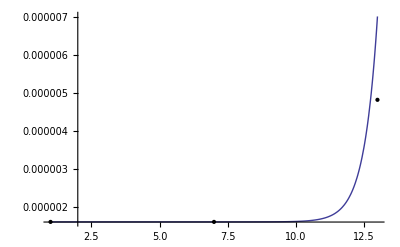

```mathematica
Block[{pg=3.2 10^-6.3,hb=9.4 10^-6.3,h2=9.62 10^-6.3,n=13},Plot[bkt2[n][j,{pg,hb,h2}],{j,1,n},PlotRange->All,Epilog->{PointSize[Large],Point[{1,pg}],Point[{(n+1)/2,hb h2+(1-hb) pg}],Point[{n,h2}]}]]
```

Linear Interpolation model.  Have constraints:  0<h0,h1<1.

```mathematica
liexpr=Simplify[h0(j-n)/(1-n)+h1 (j-1)/(n-1)]
```

(h1 (-1+j)+h0 (-j+n))/(-1+n)

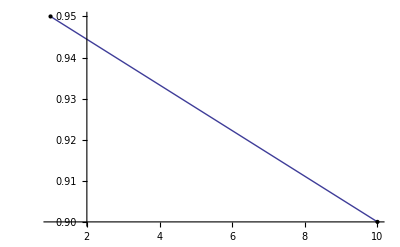

```mathematica
Block[{h0=0.95,h1=.9,n=10},Plot[linear[n][j,{h0,h1}],{j,1,n},Epilog->{PointSize[Large],Point[{1,h0}],Point[{n,h1}]}]]
```

Quadratic Interpolation model.  Have constraints:  0<h0,h1,h2<1.  However, it is easy for the interpolated quadratic to exceed the bounds [0,1].

```mathematica
qiexpr=Simplify[h0(j-(n+1)/2)(j-n)/((1-(n+1)/2) (1-n))+h1 (j-1) (j-n)/(((n+1)/2-1)((n+1)/2-n))+h2 (j-1)(j-(n+1)/2)/((n-1) (n-(n+1)/2))]
```

(h2 (-1+j) (-1+2 j-n)-(j-n) (4 h1 (-1+j)+h0 (1-2 j+n)))/(-1+n)^2

```mathematica
qmin=Simplify[Solve[D[qiexpr,j]==0,j]][[1]]
```

{j→(h0+3 h0 n-4 h1 (1+n)+h2 (3+n))/(4 (h0-2 h1+h2))}

```mathematica
j/.qmin
```

(h0 + 3*h0*n - 4*h1*(1 + n) + h2*(3 + n))/(4*(h0 - 2*h1 + h2))

```mathematica
Simplify[qiexpr/.qmin]
```

-((h0^2 + (-4*h1 + h2)^2 - 2*h0*(4*h1 + h2))/(8*(h0 - 2*h1 + h2)))

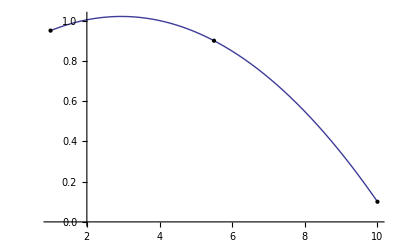

```mathematica
Block[{h0=0.95,h1=.9,h2=0.1,n=10},Plot[quadratic[n][j,{h0,h1,h2}],{j,1,n},Epilog->{PointSize[Large],Point[{1,h0}],Point[{(n+1)/2,h1}],Point[{n,h2}]}]]
```

### Models and Fitting routines

```mathematica
(* For these functions, n goes from 1 to number of steps *)
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1);(* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
(* Need (n-1) so ps and pg bounds ares simple *)
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b (n-1)];
(* Interpolation form:  this allows for a wider range of model parameters, although canonical parameters may stray out of normal bounds. *)bkt2[n_][j_, {pg_, hb_, h2_}] :=  Block[{y =( 1-hb)/hb, 
    ps =1-(h2 hb^2-pg(1-hb)^2 )/(2 hb-1)}, 
   1 - ps - (1 - ps - pg) y^(2(j - 1)/(n - 1))]
(* Linear model in interpolation form. *)
linear[n_][j_,{h0_,h1_}]:=(h1 (j-1)+h0 (n-j))/(n-1)
(* Quadratic model in interpolaation form. *)
quadratic[n_][j_, {h0_, h1_, h2_}] :=
  (h2*(-1 + j)*(-1 + 2*j - n) - (j - n)*(4*h1*(-1 + j) + 
      h0*(1 - 2*j + n)))/(-1 + n)^2
```

```mathematica
(* For each model, specify bit strings that fit model exactly.  Sometimes, these are problematic for numerical minimization. *)
isStep[data_]:=MatchQ[data,{0..,1..}|{1..,0..}];
isConstant[data_]:=MatchQ[data,{0..|1..}];
Clear[perfectFit]; (* Need to clear before updating so catch-all is at end. *)
perfectFit[logistic|step,data_]:=isConstant[data]||isStep[data];
perfectFit[bkt,data_]:=isConstant[Drop[data,1]];
perfectFit[bkt2,data_]:=isConstant[Drop[data,1]]||isConstant[Drop[data,-1]];
perfectFit[linear|quadratic,data_]:=isConstant[data];
perfectFit[__]:=False  (* catch-all *)
```

```mathematica
(* AIC for step model calculated explicitly. *)
stepFit[data_,i_]:=Block[{l0=Count[Take[data,i-1],0],l1=Count[Take[data,i-1],1],u0=Count[Drop[data,i-1],0],u1=Count[Drop[data,i-1],1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];logLike];
stepGain[data_,i_]:=If[i==1,0,Block[{l0=Count[Take[data,i-1],0],l1=Count[Take[data,i-1],1],u0=Count[Drop[data,i-1],0],u1=Count[Drop[data,i-1],1]},If[l0+l1>0 && u0+u1>0,1-l1/(l0+l1)]-u0/(u0+u1)]];
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{logLike=stepFit[data,i]},If[logLike>best,best=logLike;lBest=i]],{i,Length[data]}];
(* Not clear if this is really 3 parameters when data is short *)If[Length[data]≥3,2*3-2*N[best]]]
```

AIC for constant model (one parameter) calculated explicitly.  Since this is a special case of the other three models, the other models should never have a worse log likelihood fit.

```mathematica
constantFit[data_]:=Block[{u0=Count[data,0],u1=Count[data,1],s},s=u0/(u0+u1);2*1-2*(If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0])];
halfFit[data_]:=2*0-2*Length[data]*Log[1/2]
```

```mathematica
(* Akaike weights for step model when all L are equally probable. *)
avgWeights[n_]:=Table[If[i==1,Exp[1],1],{i,n}]/(Exp[1]+n-1)
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle -Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i,params],1-model[i,params]]],{i,Length[data]}]
(* If you plot the likelihood as a function of parameter, you see a space with many valleys, presumably one per data point.  Thus we make the number of starting points propotional to length of the dataset. *)defaultMethod={"RandomSearch","SearchPoints"->Max[10 #1 (* Length[vars] *),2#2 (*Length[data]*),100],Method->"ConjugateGradient"}&;
maxer[model_,vars_,constraints_,data_,method_:"DifferentialEvolution"]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All of the functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
perfectFit[model,data],2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,
Method->If[Head[method]===Function,method[Length[vars],Length[data]],method]]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
logisticConstraints[x_]:=Block[{delta=15.,ones=Position[x,1,1],zeros=Position[x,0,1]},Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta≤ mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& -2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]]≤b≤ 2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15.},Exp[-delta]≤pg≤1-Exp[-delta] && Exp[-delta]≤ps≤1-Exp[-delta]  && 0≤b≤delta]
```

```mathematica
bkt2Constraints[_]:=Block[{delta=15.},Exp[-delta]≤pg≤1-Exp[-delta] &&(* Since hb^2 and (1-hb)^2 enter into the formula for h1, need larger bound for limit. *) 
Exp[-delta/2]≤hb≤1-Exp[-delta/2] &&Exp[-delta]≤h2≤1-Exp[-delta]  ]
```

```mathematica
linearConstraints[_]:=Block[{delta=15.},Exp[-delta] ≤h0≤1-Exp[-delta]&& Exp[-delta] ≤h1<= 1-Exp[-delta]]
```

```mathematica
quadraticConstraints[x_]:=Block[{delta=15.,n=Length[x]},Exp[-delta] ≤h0≤1-Exp[-delta]&& Exp[-delta]≤h1≤1-Exp[-delta]&& Exp[-delta]≤h2≤1-Exp[-delta] && 
(* Test that the vertex of the quadratic is either outside of the region 1≤j≤n or has a value between zero and 1 *)(Not[0≤( h0 + 3*h0*n - 4*h1*(1 + n) + h2*(3 + n))/(4*(h0 - 2*h1 + h2))≤n]  ||  0≤  -((h0^2 + (-4*h1 + h2)^2 - 2*h0*(4*h1 + h2))/(8*(h0 - 2*h1 + h2)))≤1)]
```

Correction to get AIC_c

```mathematica
aicCorrection[k_,n_]:=2 k (k+1)/(n-k-1)
```

### Generate random data

Best possible data set

```mathematica
data["ideal",n_:1]:=Flatten[Table[Map[Block[{nd=Length[#]-3,nn},nn=If[nd==1,1,RandomInteger[nd-2]+1];Join[{Null,Null,Null},Table[0,{nn}],Table[1,{nd-nn}]]]&,data["student"]],{n}],1];
```

Make random data, 50 % correct, even distribution if possible.

```mathematica
data["random",n_,length_:Infinity]:=
If[length≥2^n,
Table[Join[{Null,Null,Null},IntegerDigits[i-1,2,n]],{i,2^n}],Table[Join[{Null,Null,Null},Table[RandomInteger[],{n}]],{length}]];
```

Take student data and reorder steps randomly.

```mathematica
data["reorder",n_:1]:=Flatten[Table[Map[Join[{Null,Null,Null},RandomSample[Drop[#,3]]]&,data["student"]],{n}],1];
```

Make exponential data

```mathematica
data["exponential",n_,length_]:=Table[Join[{Null,Null,Null},Block[{ps=RandomReal[0.5],pg=RandomReal[0.5],h=RandomReal[]},Table[If[RandomReal[]<1-ps-(1-ps-pg) h^( 2 (j-1)/(n-1)),0,1],{j,n}]]],{length}];
```

Make random data with triangle probability distribution.  The idea here is that none of the three models will fit this distribution well.

```mathematica
data["triangle",n_,length_]:=Table[Join[{Null,Null,Null},Table[If[Random[]*(n-1)<2*Min[i-1,n-i],1,0],{i,n}]],{length}];
```

Make step data.  This corresponds to the "ideal" dataset in the paper except that the distribution is even.

```mathematica
data["step",n_]:=Table[Join[{Null,Null,Null},Table[If[j<i,0,1],{i,n}]],{j,n-1}];
```

### Compare different minimzation techniques

Using BKT as test function since that is what others are using and seems to be hardest to do numerically.  If there are many data points (n>50) then all the methods converge to same result.  If I look at 10 to 30 data points, then the methods converge differently.  It seems that DifferentialEvolution is the winner:  it never does worse than the other methods.  However, it can be slow.

```mathematica
dta=data["randomC",50,6];
```

```mathematica
methodist[method_]:=Timing[Map[maxer[bkt2[Length[#]-3],{pg,hb,h2},bkt2Constraints,Drop[#,3],method]&,dta]]
```

```mathematica
methodist["DifferentialEvolution"]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.56115,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist["NelderMead"]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.40979,{36.4521,38.7306,39.0222,33.7174,38.3756,40.0174}}

```mathematica
methodist["RandomSearch"]
```

{2.06369,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist["SimulatedAnnealing"]
```

{1.53477,{36.4521,38.7306,39.0222,33.7174,38.6514,40.0174}}

```mathematica
methodist[{"RandomSearch",Method->"ConjugateGradient"}]
```

{2.53062,{36.4521,38.7306,39.3852,33.7174,38.3756,39.9536}}

#### Optimize parameters for NelderMead

```mathematica
methodist[{"NelderMead","ShrinkRatio"->0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.35879,{36.4521,38.7306,39.0222,33.7174,38.3756,40.0174}}

#### Optimize parameters for DifferentialEvolution

See discussion at http : // mathematica.stackexchange.com/questions/2309/problem - with - nonlinearmodelfit
Scaling factor 0.6 and Cross probability 0.5 are optimal:

```mathematica
methodist[{"DifferentialEvolution","ScalingFactor"->0.7}]
```

{5.51816,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","ScalingFactor"->0.6}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.59315,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","ScalingFactor"->0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.53716,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","CrossProbability"->0.4}]
```

{5.44117,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","CrossProbability"->0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.63214,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","CrossProbability"->0.6}]
```

{5.49716,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","SearchPoints"-> #1}&]
```

{1.94471,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","SearchPoints"->2 #1}&]
```

{1.9427,{36.4521,39.6115,39.0222,33.7174,38.6514,40.0174}}

```mathematica
methodist[{"DifferentialEvolution","SearchPoints"->5 #1}&]
```

{3.07953,{36.4521,38.7306,39.0222,33.7174,38.6514,40.0174}}

```mathematica
methodist[{"DifferentialEvolution","SearchPoints"->10 #1}&]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.62415,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","SearchPoints"->15 #1}&]
```

{7.71383,{36.4521,38.7306,39.0222,33.7174,38.3756,39.9536}}

```mathematica
methodist[{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"QuasiNewton"}}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.57015,{68.8582,71.1301,74.4071,69.1199,69.5571,72.7989}}

```mathematica
methodist[{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"LevenbergMarquardt"}}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.51916,{68.8582,71.1301,74.4071,69.1199,69.5571,72.7989}}

```mathematica
methodist[{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"ConjugateGradient"}}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.57415,{68.8582,71.1301,74.4071,69.1199,69.5571,72.7989}}

```mathematica
methodist[{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"PrincipalAxis"}}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.77112,{68.8582,71.1301,74.4071,69.1199,69.5571,72.7989}}

```mathematica
methodist[{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"Newton"}}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.77012,{68.8582,71.1301,74.4071,69.1199,69.5571,72.7989}}

```mathematica
methodist[{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"InteriorPoint"}}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.48517,{68.8582,71.1301,74.4071,69.1199,69.5571,72.7989}}

### Scan parameter space to find local minima

fitting to random data:
For bkt2 and 10 steps, we see generally 2 or 3 local minima, mostly sitting on the boundary.
For bkt2 and 15 steps, we see 2 points both sitting on boundary.
For bkt2 and 25 steps, we see 9 local minima with only 3 sitting on boundary. Two local minima with one on boundary.  Three local minima with one on boundary.
For bkt2 and 50 steps, we see 4 local minima with 2 sitting on boundary.

Fitting to exponential data :
For bkt2 and 15 steps, we see 2 points both sitting on boundary.
{0,1,0,0,1,0,1,0,0,0,0,0,0,0,1} gives 52 local minima scattered throughout region, with maybe 5 on boundary.

```mathematica
scan=Block[{n=15,dx=0.1},Block[{data=Drop[data["exponential",n,1][[1]],3],model=bkt2[n],vars={pg,hb,h2}},
Print["data is ",data];
Table[(*Print["  starting ",{x1,x2,x3}];*)FindMaximum[{logProb[model,vars,data],bkt2Constraints[data]},Transpose[{vars,{x1,x2,x3}}]],{x1,dx/2,1-dx/2,dx},{x2,dx/2,1-dx/2,dx},{x3,dx/2,1-dx/2,dx}]]];
```

data is {0,1,0,0,1,0,1,0,0,0,0,0,0,0,1}

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {8.84185, 3.33934×10^-16, 2.32393}, is returned.

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {6.64552, 5.54244×10^-16, 1.86321}, is returned.

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.771935, 2.18487, 0.165209}, is returned.

General::stop: Further output of FindMaximum :: eit will be suppressed during this calculation.

```mathematica
localMax=DeleteDuplicates[Map[{pg,hb,h2}/.#[[2]]&,Flatten[scan,2]],(Total[Abs[#1-#2]]<10^-6)&]
```

{{0.393327,0.765066,0.202921},{0.21423,0.000553084,1.},{0.21423,0.000553085,0.999999},{0.05,0.45,0.75},{0.05,0.65,0.65},{0.232128,0.159121,0.556625},{0.393328,0.765068,0.202921},{0.19878,0.0731197,0.835939},{0.25,0.05,0.85},{0.273892,0.0965774,0.685602},{0.45,0.05,0.85},{0.276801,0.133194,0.554716},{0.21423,0.000553088,0.999986},{0.21423,0.000553086,0.999994},{0.252448,0.23906,0.882872},{0.45,0.65,0.65},{0.247359,0.141913,0.804812},{0.21423,0.000553087,0.999991},{0.213273,0.105015,0.749709},{0.197627,0.113272,0.853587},{0.136624,0.0350905,0.986146},{0.267609,0.0379147,0.668045},{0.325807,0.272898,0.856736},{0.237153,0.0472865,0.414752},{0.241251,0.114961,0.619024},{0.194732,0.107081,0.980884},{0.272171,0.207606,0.611888},{0.267627,0.154928,0.81551},{0.239668,0.136042,0.772556},{0.55,0.85,0.65},{0.237075,0.180393,0.871487},{0.207304,0.0683397,0.893312},{0.181266,0.0869653,0.966475},{0.229261,0.0124864,0.566099},{0.256026,0.12601,0.633086},{0.322733,0.252638,0.821022},{0.277481,0.162874,0.602389},{0.30314,0.284264,0.727628},{0.257536,0.141689,0.66442},{0.393328,0.765066,0.202921},{0.319962,0.168369,0.662873},{0.297656,0.135838,0.719935},{0.289862,0.0368903,0.6581},{0.306304,0.195513,0.85752},{0.322225,0.121748,0.745568},{0.214231,0.000553089,0.999985},{0.335128,0.184384,0.686293},{0.441875,0.234001,0.61649},{0.21423,0.000553085,0.999997},{0.30094,0.155333,0.871622},{0.303065,0.210531,0.965443},{0.456706,0.214385,0.641986}}

```mathematica
Length[localMax]
```

52

```mathematica
ListPointPlot3D[localMax,PlotStyle->{PointSize[Large]},AxesLabel->{pg,hb,h2},PlotRange->{{0,1},{0,1},{0,1}}]
```

-Graphics3D-

### Generate full tables of AIC' s

```mathematica
generateAICs[set__]:=Prepend[Map[{Print[{set,#[[1]],#[[3]]}];#[[1]],#[[3]],Length[Drop[#,3]],maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],stepFit[Drop[#,3]],maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],maxer[bkt2[Length[Drop[#,3]]],{pg,hb,h2},bkt2Constraints,Drop[#,3]],
halfFit[Drop[#,3]],constantFit[Drop[#,3]],maxer[linear[Length[Drop[#,3]]],{h0,h1},linearConstraints,Drop[#,3]],maxer[quadratic[Length[Drop[#,3]]],{h0,h1,h2},quadraticConstraints,Drop[#,3]]}&,data[set]],
{"KC","student","length","logistic","step","bkt","bkt2","half","constant","linear","quadratic"}]
```

This takes a long time to calculate.  Do as batch process; see file "generate-fits.m"

```mathematica
allValues=generateAICs["student"];
Save["fitAll.m",allValues]
```

```mathematica
Table[randomValues[i]=generateAICs["randomC",i,100],{i,10,50,10}];Save["fitRandomData.m",randomValues]
```

```mathematica
Table[exponentialValues[i]=generateAICs["exponential",i,100],{i,10,50,10}];Save["fitExponentialData.m",exponentialValues]
```

```mathematica
Table[randomValues[i] = generateAICs["random", i, 100], {i, 10, 50, 10}]; 
  Save["fitRandomData.m", randomValues]
```

```mathematica
Table[stepValues[i] = generateAICs["step", i], {i, 10, 50, 10}]; 
  Save["fitStepData.m", stepValues]
```

{step,10,Null,Null}

NMaximize::nrnum: The function value 2591.44  - 9.42478\ ⅈ
 is not a real number at {h0, h1, h2} = {0.0317172, 0.98895, 0.820346}.

{step,10,Null,Null}

NMaximize::nrnum: The function value 192.146  - 3.14159\ ⅈ
 is not a real number at {h0, h1, h2} = {0.02684, 0.10264, 0.821049}.

{step,10,Null,Null}

NMaximize::nrnum: The function value 318.203  - 3.14159\ ⅈ
 is not a real number at {h0, h1, h2} = {0.049217, 0.0774203, 0.714443}.

General::stop: Further output of NMaximize :: nrnum will be suppressed during this calculation.

{step,10,Null,Null}

{step,10,Null,Null}

{step,10,Null,Null}

«3 more identical outputs»

{step,20,Null,Null}

{step,20,Null,Null}

{step,20,Null,Null}

«16 more identical outputs»

{step,30,Null,Null}

{step,30,Null,Null}

{step,30,Null,Null}

«4 more identical outputs»

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{step,30,Null,Null}

{step,30,Null,Null}

{step,30,Null,Null}

«19 more identical outputs»

{step,40,Null,Null}

{step,40,Null,Null}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{step,40,Null,Null}

{step,40,Null,Null}

{step,40,Null,Null}

«2 more identical outputs»

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

{step,40,Null,Null}

{step,40,Null,Null}

{step,40,Null,Null}

«29 more identical outputs»

{step,50,Null,Null}

{step,50,Null,Null}

{step,50,Null,Null}

«46 more identical outputs»

```mathematica
Table[exponentialValues[i] = generateAICs["exponential", i, 100], {i, 10, 50, 10}]; 
  Save["fitExponentialData.m", exponentialValues]
```

```mathematica
triangleValues10=generateAICs["triangle",10,100];
triangleValues25=generateAICs["triangle",25,100];
triangleValues50=generateAICs["triangle",50,100];
Save["fitTriangles.m",{triangleValues10,triangleValues25,triangleValues50}]
```

### Plots of functions

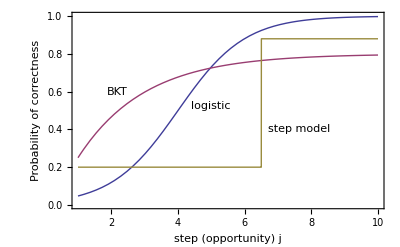

```mathematica
pModels=Plot[{logistic[x,{4,1}],bkt[x,{.5,.25,.2}],step[x,{7,.2,.12}]},{x,1,10},PlotRange->{0,1},Axes->False,Frame->True,Exclusions->None,FrameLabel->{"step (opportunity) j","Probability of correctness"},
	Epilog->{Text["BKT",{2.5,0.57},{1,-1}],Text["logistic",{4.4,.55},{-1,1}],Text["step model",{6.7,.4},{-1,0}](*,Text["L",{7,.2},{0,-1}],{Dashed,Line[{{7,0},{7,.2}}]}*)},
PlotStyle->{Thick},BaseStyle->If[False(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->18}]]
```

4.62 in or 332 points

```mathematica
Export["three-models.png",pModels,ImageSize->400]
```

three-models.png

```mathematica
Export["three-models.eps",pModels,ImageSize->figureWidth]
```

three-models.eps

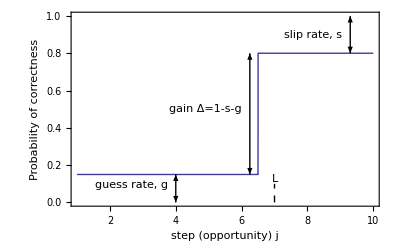

```mathematica
oModel=Block[{ll=7,g=0.15,s=0.2,ga=4,arrow=9.3},Plot[step[x,{ll,g,s}],{x,1,10},PlotRange->{0,1},Axes->False,Frame->True,Exclusions->None,FrameLabel->{"step (opportunity) j","Probability of correctness"},
	Epilog->{Text["guess rate, g",{ga-.25,g-0.03},{1,1}],If[False,{},{Arrowheads[{-.04,.04}],Arrow[{{ll-3/4,g},{ll-3/4,1-s}}],Text["gain Δ=1-s-g",{ll-1,1/2},{1,0}]}],{Dashed,Line[{{ll,0},{ll,.1}}]},Text["L",{ll,0.1},{0,-1}],
{Arrowheads[{-.04,.04}],Arrow[{{ga,0},{ga,g}}],Arrow[{{arrow,1-s},{arrow,1}}]},Text["slip rate, s",{arrow-.25,1-s/2},{1,0}](*,Text["L",{7,.2},{0,-1}],{Dashed,Line[{{7,0},{7,.2}}]}*)},
PlotStyle->{Thick},BaseStyle->If[False(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->18}]]]
```

4.62 in or 332 points

```mathematica
Export["step-model.eps",oModel,ImageSize->figureWidth]
```

step-model.eps

Width 396 =  5.5 in.  Include gain.

```mathematica
Export["step-model.png",oModel,ImageSize->396]
```

step-model.png

```mathematica
oModel=Block[{ll=7,g=0.15,s=0.2,ga=4,arrow=9.3},Plot[step[x,{ll,g,s}],{x,1,10},PlotRange->{0,1},Axes->False,Frame->True,Exclusions->None,FrameLabel->{"step (opportunity) j","Probability of correctness"},
	Epilog->{Text["guess rate, g",{ga-.25,g-0.03},{1,1}],{Dashed,Line[{{ll,0},{ll,.1}}]},Text["L",{ll,0.1},{0,-1}],
{Arrowheads[{-.04,.04}],Arrow[{{ga,0},{ga,g}}],Arrow[{{arrow,1-s},{arrow,1}}]},Text["slip rate, s",{arrow-.25,1-s/2},{1,0}](*,Text["L",{7,.2},{0,-1}],{Dashed,Line[{{7,0},{7,.2}}]}*)},
PlotStyle->{Thick},BaseStyle->If[False(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->18}]]]
```

```mathematica
st[l_,g_,s_]:={Hue[1-l/6],Text["L="<>ToString[l],{l,1/2}],If[l==1,(* No learning case, ignore guess rate *)Line[{{l-3/2,1-s},{l+1,1-s}}],Line[{{l-3/2,g},{l-1/2,g},{l-1/2,1-s},{l+1,1-s}}]]}
```

This is for presentation, to explain submodels

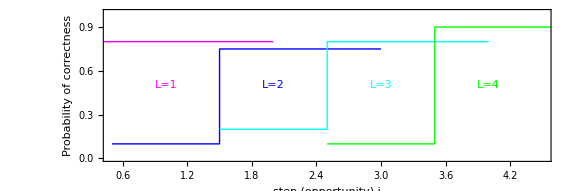

```mathematica
submodels=Block[{ll=7,g=0.15,s=0.2,ga=4,arrow=9.3},Plot[-1,{x,1/2,5-1/2},PlotRange->{0,1},Axes->False,Frame->True,Exclusions->None,AspectRatio->1/3,FrameLabel->{"step (opportunity) j","Probability of correctness"},
	Epilog->{st[1,.25,.2],st[2,.1,.25],st[3,.2,.2],st[4,.1,.1]},
PlotStyle->{Thick},BaseStyle->If[False(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->18}]]]
```

Width 576 = 8 in.

```mathematica
Export["submodels.png",submodels,ImageSize->576]
```

submodels.png

### Compare three models: logistic, step, and BKT

Logistic, step model, Baysian Knowledge Tracing

```mathematica
Get["fitAll.m"];First[allValues]
```

{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic}

```mathematica
Get["fitRandomData.m"];First[randomValues[50]]
```

{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic}

```mathematica
Get["fitStepData.m"];First[stepValues[50]]
```

{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic}

```mathematica
Get["fitExponentialData.m"];First[exponentialValues[50]]
```

{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic}

Test that fits were successful

Here, set cutValues to the desired variable to get a particular dataset.

```mathematica
cutValues[ss_]:=Select[Rest[ss],#[[3]]≥10 &]
```

```mathematica
Table[Select[randomValues[i],Not[MatchQ[N[Drop[#,3]],{__?NumberQ}]]&],{i,10,50,10}]
```

{{{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic},{Null,Null,10,16.326,14.3758,16.7609,16.7609,20 Log[2],2+20 Log[2],16.3446,False},{Null,Null,10,16.326,14.3758,16.7609,16.7609,20 Log[2],2+20 Log[2],16.3446,False},{Null,Null,10,16.326,14.3758,16.7609,16.7609,20 Log[2],2+20 Log[2],16.3446,False},{Null,Null,10,16.326,14.3758,16.7609,16.7609,20 Log[2],2+20 Log[2],16.3446,False},{Null,Null,10,16.326,14.3758,16.7609,16.7609,20 Log[2],2+20 Log[2],16.3446,False},{Null,Null,10,16.326,14.3758,16.7609,16.7609,20 Log[2],2+20 Log[2],16.3446,False}},{{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic},{Null,Null,20,30.5621,29.0649,31.0816,31.0816,40 Log[2],2-2 (-11 Log[20/11]-9 Log[20/9]),30.5219,False},{Null,Null,20,29.5237,29.6865,29.6989,30.965,40 Log[2],2-2 (-13 Log[20/13]-7 Log[20/7]),29.518,False}},{{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic}},{{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic}},{{KC,student,length,logistic,step,bkt,bkt2,half,constant,linear,quadratic}}}

There are a couple of quadratic fits that failed.

```mathematica
TableForm[Table[Map[Mean,Transpose[Map[N[Drop[Drop[#,3],-1]-#[[8]]]&,Rest[randomValues[i]]]]],{i,10,50,10}]]
```

1.62549 | 1.22732 | 2.90407 | 2.58661 | 0. | 0.928544 | 1.69604
1.87372 | 0.76923 | 2.84892 | 2.64393 | 0. | 0.972803 | 1.85137
1.9277 | 0.533177 | 2.80073 | 2.63925 | 0. | 0.99835 | 1.91263
1.96795 | 0.404238 | 2.79561 | 2.68965 | 0. | 0.999594 | 1.96053
1.9033 | 0.21855 | 2.69651 | 2.6239 | 0. | 0.949941 | 1.89736

```mathematica
Histogram[Transpose[Map[(Drop[#,3]-#[[8]])&,Rest[randomValues[20]]]][[1]],50,PlotRange->All]
```

-Graphics-

```mathematica
testFits[ss_]:=(Map[(* Subtract off the 2K since we want to compare log likelihoods. *)Block[{x=#[[8]]-2*1},If[#[[4]]-2*2>x,Print["Bad aics for logistic ",#]];If[#[[5]]-2*3>x,Print["Bad aics for step ",#]];If[#[[6]]-2*3>x,Print["Bad aics for bkt ",#]];
If[#[[7]]-2*3>x,Print["Bad aics for bkt2 ",#]];
(* Don't compare with itself *)If[#[[9]]-2*2>x,Print["Bad aics for linear ",#]];
If[ #[[10]]-2*3>x,Print["Bad aics for quadratic ",#]]]&,cutValues[ss]];)
```

```mathematica
distinctCounts[ss_]:={Length[cutValues[ss]],Length[Union[Map[First,cutValues[ss]]]],Length[Union[Map[#[[2]]&,cutValues[ss]]]]}
```

```mathematica
aics[ss_]:=Map[{#[[4]]+aicCorrection[2,#[[3]]],#[[5]]+aicCorrection[3,#[[3]]],#[[6]]+aicCorrection[3,#[[3]]],#[[7]]+aicCorrection[3,#[[3]]],
#[[8]]+aicCorrection[1,#[[3]]],#[[9]]+aicCorrection[2,#[[3]]],#[[10]]+aicCorrection[3,#[[3]]]}&,cutValues[ss]];
```

SetDelayed::write: Tag List in {{1, 13.0904}, {2, 13.5607}, {3, 11.6382}, {4, 9.00402}, {5, 12.9974}, {6, 14.5492}, {7, 11.6382}, {8, 13.5607}}[ss_] is Protected.

```mathematica
aics2[ss_]:=Map[Drop[Drop[#,3],-1]&,cutValues[ss]];
```

Convert from AIC to BIC

```mathematica
bicCorrection[k_,n_]:=-2 k+k Log[n];bics[ss_]:=Map[{#[[4]]+bicCorrection[2,#[[3]]],#[[5]]+bicCorrection[3,#[[3]]],#[[6]]+bicCorrection[3,#[[3]]],#[[7]]+bicCorrection[3,#[[3]]],
#[[8]]+bicCorrection[1,#[[3]]],#[[9]]+bicCorrection[2,#[[3]]],#[[10]]+bicCorrection[3,#[[3]]]}&,cutValues[ss]];
```

Find Akaike weights for logistic, BKT, and step, ordering by BKT value.

```mathematica
aics3[ss_]:=Sort[Map[Join[Take[#,3],Block[{y=Exp[-Take[#,{4,6}]/2]},y/Total[y]]]&,cutValues[ss]],#1[[-1]]<#2[[-1]]&];
```

```mathematica
Cases[data["student"],{"define-mass",__}]
```

Student data cases having maximum Akaike weight for BKT:
{"define-mass", "asu_9Q1920841f2ca4d1fasul1_c", "md5:1da7d76bc3d524d51da47dde26ee8f95", 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 1, 1, 0, 1, 0, 1, 1, 0, 1, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 0}
{"draw-weight", "asu_9Q1920841f2ca4d1fasul1_e", "md5:e9747bab59caf0446778cc6a65a8ac2e", 0, 1, 1, 1, 0, 1, 1, 1, 1, 1, 1, 1, 0, 1, 1, 0, 1, 1}
{"define-mass", "asu_9Q1920841f2ca4d1fasul1_c", "md5:a38723384afd4471b62218d16045a11d", 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 1, 1, 0, 1, 1, 1, 1, 1, 1, 1, 0, 1, 1, 1, 1, 1, 1, 0, 1, 0, 1}
{"write-ohms-law", "asu_9Q1920841f2ca4d1fasul1_c", "md5:a38723384afd4471b62218d16045a11d", 0, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1}
{"draw-vector-aligned-axes", "asu_9Q1920841f2ca4d1fasul1_e", "md5:e9747bab59caf0446778cc6a65a8ac2e", 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0}

```mathematica
akaikeWeights[ss_]:=Map[Block[{y=Exp[-#/2]},y/Total[y]]&,aics[ss]];
```

```mathematica
akaikeWeights2[ss_]:=Map[Block[{y=Exp[-#/2]},y/Total[y]]&,aics2[ss]];
```

```mathematica
bicWeights[ss_]:=Map[Block[{y=Exp[-#/2]},y/Total[y]]&,bics[ss]];
```

```mathematica
weightAverages[ss_]:=Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeWeights[ss]]]
```

```mathematica
weightAverages2[ss_]:=Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeWeights2[ss]]]
```

Test that numerical fits are better than constant model.

```mathematica
testFits[allValues]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[allValues].

Part::partd: Part specification allValues ⟦ 3 ⟧ is longer than depth of object.

Rest::argx: Rest called with 0 arguments; 1 argument is expected.

```mathematica
testFits[randomValues[50]]
```

```mathematica
testFits[randomValues[25]]
```

```mathematica
testFits[randomValues[10]]
```

Look at BIC

```mathematica
meanBicWeights=Transpose[Table[Map[{i,#}&,Mean[Map[(Take[#,3]/(#[[1]]+#[[2]]+#[[3]]))&,bicWeights[randomValues[i]]]]],{i,10,50,10}]]
```

{{{10,0.394965},{20,0.40961},{30,0.434694},{40,0.449931},{50,0.460664}},{{10,0.413684},{20,0.431024},{30,0.422396},{40,0.41796},{50,0.415939}},{{10,0.191351},{20,0.159365},{30,0.14291},{40,0.132109},{50,0.123397}}}

```mathematica
meanBicFits=Map[Fit[#,{1,1/n},n]&,meanBicWeights]
```

{0.465222-0.771885/n,0.422138-0.0424154/n,0.11264+0.8143/n}

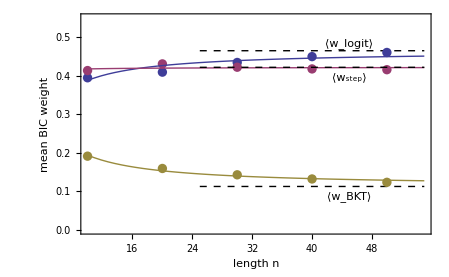

```mathematica
plotMeanBicWeights=Show[ListPlot[meanBicWeights,PlotStyle->{PointSize[0.015]}],Plot[meanBicFits,{n,10,55}],PlotRange->{0,.55},Epilog->{{Dashed,Map[Line[{{25,#},{55,#}}]&,meanBicFits/.n->Infinity]},Text[AngleBracket[Subscript[w,logit]],{45,.47},{0,-1}],Text[AngleBracket[Subscript[w,step]],{45,.41},{0,1}],Text[AngleBracket[Subscript[w,BKT]],{45,.10},{0,1}]},Axes->False,Frame->True,FrameLabel->{"length n","mean BIC weight"},BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

```mathematica
meanWeights=Transpose[Table[Map[{i,#}&,Mean[Map[(Take[#,3]/(#[[1]]+#[[2]]+#[[3]]))&,akaikeWeights2[randomValues[i]]]]],{i,10,50,10}]]
```

{{{10,0.361067},{20,0.302742},{30,0.285498},{40,0.272551},{50,0.262178}},{{10,0.436473},{20,0.50561},{30,0.528632},{40,0.545736},{50,0.560818}},{{10,0.20246},{20,0.191647},{30,0.18587},{40,0.181712},{50,0.177004}}}

```mathematica
meanFits=Map[Fit[#,{1,1/n},n]&,meanWeights]
```

{0.24205+1.19907/n,0.583665-1.49367/n,0.174285+0.294596/n}

Sanity check:  the Fits add up to one at all n :

```mathematica
Total[meanFits]
```

1.-(1.59872×10^-14)/n

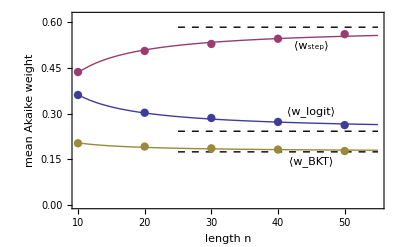

```mathematica
plotMeanWeights=Show[ListPlot[meanWeights,PlotStyle->{PointSize[0.015]}],Plot[meanFits,{n,10,55}],PlotRange->{0,.62},Epilog->{{Dashed,Map[Line[{{25,#},{55,#}}]&,meanFits/.n->Infinity]},Text[AngleBracket[Subscript[w,logit]],{45,.29},{0,-1}],Text[AngleBracket[Subscript[w,step]],{45,.54},{0,1}],Text[AngleBracket[Subscript[w,BKT]],{45,.16},{0,1}]},Axes->False,Frame->True,FrameLabel->{"length n","mean Akaike weight"},BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

```mathematica
Export["mean-weights.eps",plotMeanWeights,ImageSize->figureWidth]
```

mean-weights.eps

```mathematica
peakBicWeights=Transpose[Table[Map[{i,#}&,cutOutlierMode[Map[(Take[#,3]/(#[[1]]+#[[2]]+#[[3]]))&,bicWeights[randomValues[i]]]]],{i,10,50,10}]]
```

{{{10,0.383989},{20,0.489162},{30,0.519099},{40,0.535366},{50,0.57481}},{{10,0.38721},{20,0.32591},{30,0.299918},{40,0.290343},{50,0.281291}},{{10,0.228801},{20,0.184928},{30,0.180984},{40,0.174291},{50,0.143899}}}

```mathematica
peakBicFits=Map[Fit[#,{1,1/n},n]&,peakBicWeights]
```

{0.600705-2.19459/n,0.256917+1.31424/n,0.142378+0.880351/n}

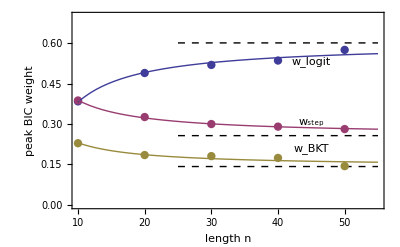

```mathematica
plotPeakBicWeights=Show[ListPlot[peakBicWeights,PlotStyle->{PointSize[0.015]}],Plot[peakBicFits,{n,10,55}],PlotRange->{0,.7},Epilog->{{Dashed,Map[Line[{{25,#},{55,#}}]&,peakBicFits/.n->Infinity]},Text[Subscript[w,logit],{45,.55},{0,1}],Text[Subscript[w,step],{45,.29},{0,-1}],Text[Subscript[w,BKT],{45,.23},{0,1}]},Axes->False,Frame->True,FrameLabel->{"length n","peak BIC weight"},BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

```mathematica
peakWeights=Transpose[Table[Map[{i,#}&,cutOutlierMode[Map[(Take[#,3]/(#[[1]]+#[[2]]+#[[3]]))&,akaikeWeights2[randomValues[i]]]]],{i,10,50,10}]]
```

{{{10,0.348885},{20,0.367903},{30,0.348436},{40,0.314452},{50,0.336677}},{{10,0.409276},{20,0.403272},{30,0.405641},{40,0.439112},{50,0.440708}},{{10,0.241839},{20,0.228825},{30,0.245923},{40,0.246437},{50,0.222614}}}

```mathematica
peakFits=Map[Fit[#,{1,1/n},n]&,peakWeights]
```

{0.331196+0.264416/n,0.434841-0.333714/n,0.233963+0.0692985/n}

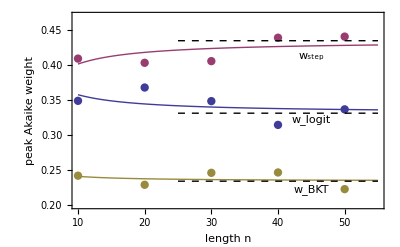

```mathematica
plotPeakWeights=Show[ListPlot[peakWeights,PlotStyle->{PointSize[0.015]}],Plot[peakFits,{n,10,55}],PlotRange->{.2,.47},Epilog->{{Dashed,Map[Line[{{25,#},{55,#}}]&,peakFits/.n->Infinity]},Text[Subscript[w,logit],{45,.33},{0,1}],Text[Subscript[w,step],{45,.42},{0,1}],Text[Subscript[w,BKT],{45,.23},{0,1}]},Axes->False,Frame->True,FrameLabel->{"length n","peak Akaike weight"},BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

```mathematica
Export["peak-weights.eps",plotPeakWeights,ImageSize->figureWidth]
```

peak-weights.eps

Point where all three models have perfect fit to data.  Logistic has higher weight since it has one fewer parameter than the other two.

```mathematica
N[{Exp[1],1}/(2+Exp[1])]
```

{0.576117,0.211942}

Common plotting stuff.

```mathematica
cross[{x_,y_},r_]:={Line[{{x,y-r},{x,y+r}}],Line[{{x-r,y},{x+r,y}}]};greenLines=Block[{delta=0.04},{{Red,Thick,cross[{1/3,1/3},delta]},(*{Purple,Circle[{Exp[1],1}/(2+Exp[1]),0.025]},*){Green,Dashed,Thick,Line[{{Exp[1],1}/(2+Exp[1]),{Exp[1],1}/(1+Exp[1])}]},
{Green,Dashed,Thick,Line[{{Exp[1],1}/(2+Exp[1]),{0,1/2}}]}}];
wBKTLines={Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],Which[i==4/5,{.3,-.3},i==3/5,{.2,-.2},True,0]+{i/2,i/2}+0.005 (* a small offset so subscript is not on line *),{0,-1},{1,-1}]},{i,1/5,1,1/5}]};
wLabels={Subscript[w,logit],Subscript[w,step]};
```

Average weights for student data.

```mathematica
Mean[Map[(Take[#,3]/(#[[1]]+#[[2]]+#[[3]]))&,akaikeWeights2[allValues]]]
```

{0.378689,0.443011,0.1783}

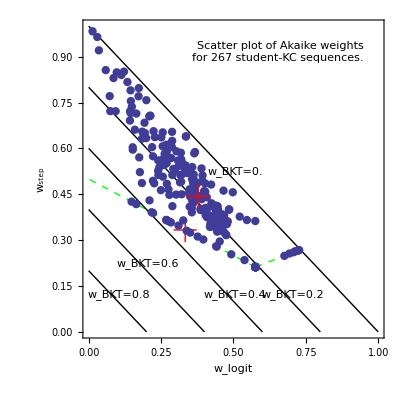

```mathematica
scatterWeights=Block[{ww=akaikeWeights2[allValues],pts},
pts=Map[({#[[1]],#[[2]]}/(#[[1]]+#[[2]]+#[[3]]))&,ww];ListPlot[pts,AspectRatio->1,PlotStyle->{PointSize[0.015]},
Epilog->{Red,Thick,cross[Mean[pts],0.04]},Prolog->Join[greenLines,wBKTLines,
{Text[Style["Scatter plot of Akaike weights\nfor "<>ToString[Length[ww]]<>" student-KC sequences." ,TextAlignment->Right],{.95,0.95},{1,1}]}],PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->wLabels,BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]]
```

4.62 in or 332 points width for presentation

```mathematica
Export["scatter-weights.png",scatterWeights,ImageSize->400]
```

scatter-weights.png

```mathematica
Export["scatter-weights.eps",scatterWeights,ImageSize->figureWidth]
```

scatter-weights.eps

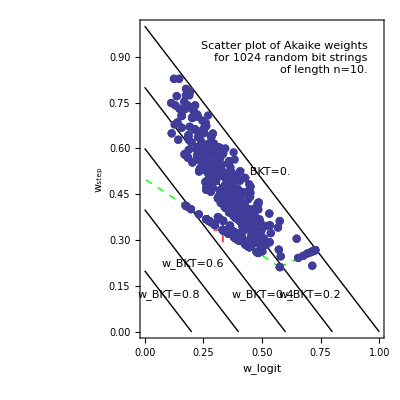

```mathematica
scatter10=Block[{ww=akaikeWeights2[randomValues[10]]},ListPlot[Map[({#[[1]],#[[2]]}/(#[[1]]+#[[2]]+#[[3]]))&,ww],AspectRatio->1,PlotStyle->{PointSize[0.015]},Prolog->Join[greenLines,wBKTLines,{Text[Style["Scatter plot of Akaike weights\nfor "<>ToString[Length[ww]]<>" random bit strings\nof length n=10." ,TextAlignment->Right],{.95,0.95},{1,1}]}],PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->wLabels,BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]]
```

```mathematica
Export["scatter10.eps",scatter10,ImageSize->figureWidth]
```

scatter10.eps

DensityHistogram is only in Mma 8, which I don' t have at home.

```mathematica
addRow[x_]:=Append[x,Table[0,{Length[x[[1]]]}]];
densityHistogram[data_,{x1_,x2_,dx_:1},{y1_,y2_,dy_:1},opts___]:=Block[{heights=addRow[Transpose[addRow[BinCounts[data,{x1,x2,dx},{y1,y2,dy}]]]]},
ListDensityPlot[heights,DataRange->{{x1,x2},{y1,y2}},PlotRange->{{x1,x2},{y1,y2},{0.0000001,Max[heights]}},InterpolationOrder->0,opts]]
```

```mathematica
randomValues[50][[2,3]]
```

50

```mathematica
densityWeights[data_]:=densityHistogram[Map[(Take[#,2]/(#[[1]]+#[[2]]+#[[3]]))&,akaikeWeights2[data]],{0,1,0.025},{0,1,0.025},FrameLabel->wLabels,Epilog->Join[greenLines,wBKTLines,{Text[Style["Density plot of Akaike weights\nfor "<>ToString[NumberForm[Length[data]-1,DigitBlock->3]]<>" random bit strings\nof length n="<>ToString[data[[2,3]]]<>"." ,TextAlignment->Right],{.95,0.95},{1,1}]}]]
```

```mathematica
densityWeights[randomValues[20]]
```

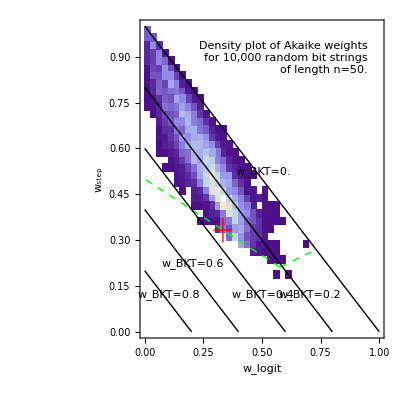

```mathematica
density50=densityWeights[randomValues[50]]
```

4.62 in or 332 points

```mathematica
Export["density50.png",density50,ImageSize->400]
```

density50.png

```mathematica
Export["density50.eps",density50,ImageSize->figureWidth]
```

density50.eps

This is just to visualize what is going on.

```mathematica
Block[{m1=1,m2=2,m3=3,names={"logit","step","bkt","bkt2","constant","linear","quadratic"}},Histogram3D[Map[{#[[m1]],#[[m2]]}/(#[[m1]]+#[[m2]]+#[[m3]])&,bicWeights[randomValues[50]]],{{0,1,0.02},{0,1,0.02}},
FaceGrids->{{{0,0,-1},{{1/3},{1/3}}}},
AxesLabel->{names[[m1]],names[[m2]]},PlotRange->{{0,1},{0,1},All}]]
```

-Graphics3D-

Histogram Akaike weights for any pair of models.

```mathematica
Block[{m1=2,m2=3,names={"logit","step","bkt","bkt2","constant","linear","quadratic"}},Histogram[Map[#[[m2]]/(#[[m1]]+#[[m2]])&,akaikeWeights2[randomValues[50]]],21,
PlotRange->{{0,1},All},
	Axes->False,Frame->True,
Epilog->{Text[names[[m1]],{0.05,7},{-1,-1}],Text[names[[m2]],{0.95,7},{1,-1}]},
FrameLabel->{"Akaike weights for "<>names[[m1]]<>" and " <>names[[m2]],"count"}]]
```

-Graphics-

### Step function model: Plot Akaike weights.

#### Distribution of weighted gains

```mathematica
Clear[weightedGains];weightedGains[set__]:=weightedGains[set]=Map[Function[{x,y},x/Apply[Plus,x] y][Table[Block[{aic=2*If[i==1,1,2]-2.*stepFit[Drop[#,3],i]},Exp[-aic/2]],{i,Length[Drop[#,3]]}],Table[stepGain[Drop[#,3],i],{i,Length[Drop[#,3]]}]]&,data[set]];
```

Numerically estimate standard deviation of weighted gain for reorder dataset where dataset has same number of sequences as student dataset.  Note the result is exactly the same as when the standard deviation of the mean is used.

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["reorder",1]},weightedGains["reorder",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

```mathematica
%/Sqrt[10]
```

0.0024483

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["random",1]},weightedGains["random",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

0.00495394

```mathematica
%/Sqrt[10]
```

0.00156657

In this case, however, we get an order of magnitude larger result from the standard deviation of the mean.

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["ideal",1]},weightedGains["ideal",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

0.000901295

```mathematica
%/Sqrt[10]
```

0.000285015

```mathematica
gStats[set__]:=Block[{xx=weightedGains[set],xxx},
xxx=Flatten[xx];{Length[xx],Length[xxx],StandardDeviation[xxx],Total[xxx]/Length[xx],StandardDeviation[xxx] Sqrt[Length[xxx]]/Length[xx]}]
```

```mathematica
gStats["student"]
```

{2017,32030,0.0730042,0.0466674,0.00647769}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=0.0466666/0.00647769},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

2.91933×10^-13

```mathematica
gStats["reorder",10]
```

{20170,320300,0.0713389,-0.00172275,0.0020017}

```mathematica
gStats["random",10]
```

{20170,320300,0.078627,0.00133552,0.0022062}

```mathematica
gStats["ideal",10]
```

{20170,320300,0.139267,0.524222,0.00390769}

```mathematica
gStats2[set__]:=Block[{xx=weightedGains[set],xxx,n},
xxx=Flatten[xx];n=Length[xx];{Length[xxx],n,N[Total[Select[xxx,#>1/2&]]/n],N[Total[Select[xxx,#<-1/2&]]/n],N[Total[Select[xxx,#>1/20&]]/n],N[Total[Select[xxx,#<-1/20&]]/n]}]
```

```mathematica
gStats2["student"]
```

{32030,2017,0.0777815,-0.0402763,0.118149,-0.0733867}

```mathematica
gStats2["reorder",10]
```

{320300,20170,0.0547603,-0.0572539,0.0908107,-0.0936874}

```mathematica
gStats2["random",10]
```

{320300,20170,0.0676128,-0.0672031,0.115425,-0.114403}

```mathematica
gStats2["ideal",10]
```

{320300,20170,0.466094,0.,0.506149,0.}

Numbers used in paper for student dataset.  Should match bins in weighed gains histogram.

```mathematica
gStats3[set__]:=Block[{xx=weightedGains[set],xxx,n},
xxx=Flatten[xx];n=Length[xx];{Length[xxx],n,Length[Select[xxx,#>1/2&]],Length[Select[xxx,#<-1/2&]],Length[Select[xxx,#>1/39&]],Length[Select[xxx,#<-1/39&]],Length[Select[xxx,Abs[#]<1/39&]]}]
```

```mathematica
gStats3["student"]
```

{32030,2017,257,133,1312,988,29730}

```mathematica
Clear[histline];histLine[set__]:=histLine[set]=Block[{xxx=Flatten[weightedGains[set]],dx=2/39},Flatten[Table[{{i-dx/2,#},{i+dx/2,#}}&[Max[0.001,Length[Select[xxx,i-dx/2≤#<i+dx/2&]]]],{i,-1+dx/2,1-dx/2,dx}],1]];
```

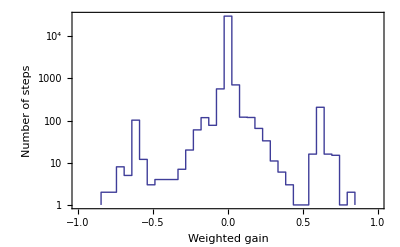

```mathematica
wgh=ListLogPlot[histLine["student"],Joined->True,Axes->False,Frame->True,FrameLabel->{"Weighted gain","Number of steps"},BaseStyle->journalStyle,PlotRange->{{-1,1},{1,All}}]
```

```mathematica
Export["weighted-gain-histogram.eps",wgh,ImageSize->figureWidth]
```

weighted-gain-histogram.eps

If I blow it up, I get the same shape!

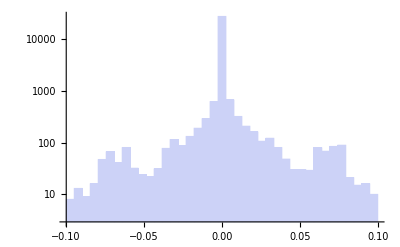

```mathematica
Histogram[Flatten[weightedGains["student"]],{-0.1,0.1,0.2/39},"LogCount"]
```

```mathematica
Needs["PlotLegends`"]
```

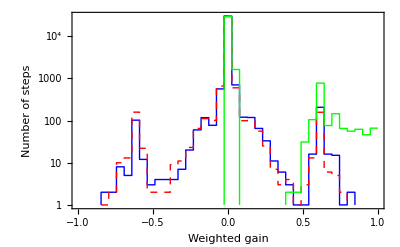

```mathematica
wgh2=ListLogPlot[{histLine["student"],histLine["reorder",1],histLine["ideal",1]},Joined->True,Axes->False,Frame->True,FrameLabel->{"Weighted gain","Number of steps"},LegendShadow->False,PlotStyle->{Blue,{Dashed,Red},{Thick,Green}},LegendSize->{0.6,.25},LegendTextSpace->4,PlotLegend->{"student dataset","random dataset","ideal dataset"},
LegendPosition->{0.23,.32},BaseStyle->journalStyle,PlotRange->{{-1,1},{1,All}}]
```

The eps file in Mathematica 7 is corrupted.

```mathematica
Export["weighted-gain-histogram2.eps",wgh2,ImageSize->figureWidth]
```

weighted-gain-histogram2.eps

Partial sum of weighed gains, adding all weighed gains whose magnitude is less than the cutoff.  This shows that most of the sum is from the weighed gains > 0.5.

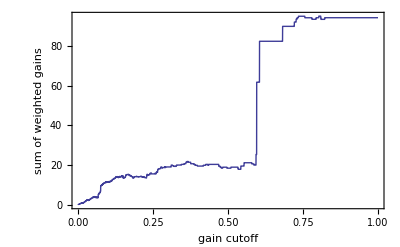

```mathematica
Block[{xxx=Flatten[weightedGains["student"]]},Plot[Total[Select[xxx,Abs[#]<x&]],{x,0,1},Axes->False,Frame->True,FrameLabel->{"gain cutoff","sum of weighted gains"},BaseStyle->{FontSize->12}]]
```

Partial sum of positive/negative weighed gains, adding all positive/negative weighed gains whose magnitude is less than the cutoff.  This shows that most of the positive/negative asymmetry is from large gains.

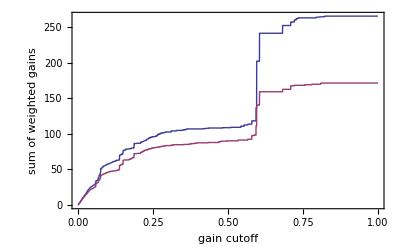

```mathematica
Block[{xxx=Flatten[weightedGains["student"]]},Plot[{Total[Select[xxx,0<#<x&]],Abs[Total[Select[xxx,0>#>-x&]]]},{x,0,1},Axes->False,Frame->True,FrameLabel->{"gain cutoff","sum of weighted gains"},BaseStyle->{FontSize->12}]]
```

#### Histogram of lengths for paper

When bins are less than an integer wide, then fall back to integer width bins.

```mathematica
histLineStudent=Block[{xxx=Map[Log[Length[Drop[#,3]]]&,data["student"]],max,dx},
max=Max[xxx];
dx=max/26;Flatten[Table[{{Max[Exp[(j-1/2)dx],j+1/2],#},{Max[Exp[(j+1/2)dx],j+3/2],#}}&[Max[0.001,Length[Select[xxx,Max[(j-1/2)dx,Log[j+1/2]]≤#<Max[(j+1/2)dx,Log[j+3/2]]&]]]],{j,0,max/dx}],1]];
```

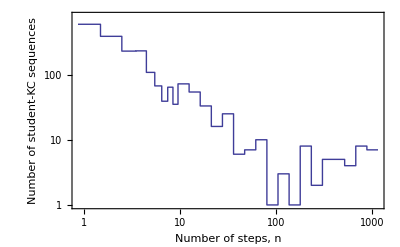

```mathematica
sklh=ListLogLogPlot[histLineStudent,Joined->True,PlotRange->{1,Max[Map[#[[2]]&,histLineStudent]] 4/3},Axes->False,Frame->True,FrameLabel->{"Number of steps, n","Number of student-KC sequences"},BaseStyle->journalStyle]
```

```mathematica
Export["student-kc-length-histogram.eps",sklh,ImageSize->figureWidth]
```

student-kc-length-histogram.eps

#### Example KC for paper

```mathematica
data1={0,0,0,1,1,0,1,1};
```

```mathematica
aics=Table[{i,N[2*If[i==1,1,2]-2*stepFit[data1,i]]},{i,Length[data1]}]
```

{{1,13.0904},{2,13.5607},{3,11.6382},{4,9.00402},{5,12.9974},{6,14.5492},{7,11.6382},{8,13.5607}}

```mathematica
gains=Table[{i,stepGain[data1,i]},{i,Length[data1]}]
```

{{1,0},{2,4/7},{3,2/3},{4,4/5},{5,1/2},{6,4/15},{7,2/3},{8,4/7}}

```mathematica
weights1=Function[x,x/Apply[Plus,x]][N[Table[Block[{aic=2*If[i==1,1,2]-2*stepFit[data1,i]},Exp[-aic/2]],{i,Length[data1]}]]]
```

{0.0626582,0.0495269,0.129514,0.483407,0.0656404,0.030213,0.129514,0.0495269}

```mathematica
weightedGains=Table[{i,stepGain[data1,i]*weights1[[i]]},{i,Length[data1]}]
```

{{1,0.},{2,0.0283011},{3,0.0863425},{4,0.386726},{5,0.0328202},{6,0.00805679},{7,0.0863425},{8,0.0283011}}

```mathematica
Total[weightedGains]
```

0.65689

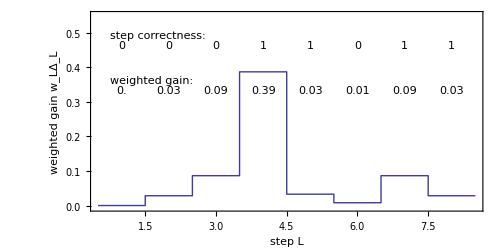

```mathematica
wgPlot=Block[{n=Length[data1],yt=0.48,y2=.35},ListPlot[Flatten[Map[{{#[[1]]-1/2,#[[2]]},{#[[1]]+1/2,#[[2]]}}&,weightedGains],1],Epilog->{Text["step correctness:",{0.75,yt},{-1,-1}],Table[Text[data1[[i]],{i,yt},{0,1}],{i,n}],
(* Optionally, print values *)If[True,{Text["weighted gain:",{0.75,y2},{-1,-1}],
	Map[Text[Round[#[[2]],0.01],{#[[1]],y2},{0,1}]&,weightedGains]},{}]},PlotRange->{{1/2,n+1/2},{-0.005,.55}},Joined->True,FrameLabel->{"step L","weighted gain  w_LΔ_L"}, AspectRatio->1/2,Axes->False,Frame->True,BaseStyle->If[False (* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->18}]]]
```

For Presentation, want width 7 in. = 504 pt. and presentation BaseStyle

```mathematica
Export["weighted-gains.png",wgPlot,ImageSize->504]
```

weighted-gains.png

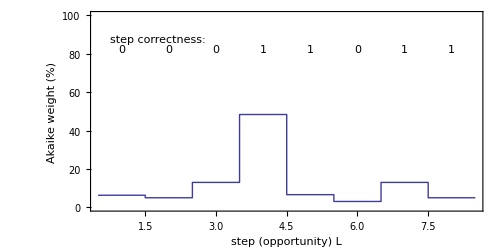

```mathematica
stepWeightsPlot=Block[{n=Length[data1],yt=85,y2=65},ListPlot[Flatten[Table[{{i-1/2,#},{i+1/2,#}}&[weights1[[i]]*100],{i,n}],1],Epilog->{Text["step correctness:",{0.75,yt},{-1,-1}],Table[Text[data1[[i]],{i,yt},{0,1}],{i,n}],
(* Don't discuss AIC values in talk *)
If[False,{Text["AIC for submodel:",{0.75,y2},{-1,-1}],
	Map[Text[Round[#[[2]],0.1],{#[[1]],y2},{0,1}]&,aics]},{}]},PlotRange->{{1/2,n+1/2},{0,100}},
Joined->True,
FrameLabel->{"step (opportunity) L","Akaike weight (%)"}, AspectRatio->1/2,Axes->False,Frame->True,BaseStyle->If[False (* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->18}]]]
```

For Presentation, want width 7 in = 504pt and presentation BaseStyle

```mathematica
Export["step-weights.png",stepWeightsPlot,ImageSize->504]
```

step-weights.png

```mathematica
Export["step-weights.eps",stepWeightsPlot,ImageSize->figureWidth]
```

step-weights.eps